# Diamond

## Convergency of k - points

-Graphics- that k

the convergency criteia is <1meV/atom.

```mathematica
SetDirectory["/home/angeldavid/wrk/Assigment/Diamond"];
```

```mathematica
file="kp.dat"
```

kp.dat

```mathematica
kpdat=Import[file]
```

{{4,-117.795},{5,-117.78},{6,-117.795},{7,-117.794},{8,-117.795},{9,-117.795},{10,-117.795},{11,-117.795},{12,-117.795},{13,-117.795}}

this is the enrgy, but i  need energy per atom (divide eneryg / 2) we have 2 atoms

```mathematica
kpdat=Import[file]//Map[#/{1,2}&,#]&
```

{{4,-58.8976},{5,-58.8901},{6,-58.8974},{7,-58.897},{8,-58.8974},{9,-58.8974},{10,-58.8974},{11,-58.8974},{12,-58.8974},{13,-58.8974}}

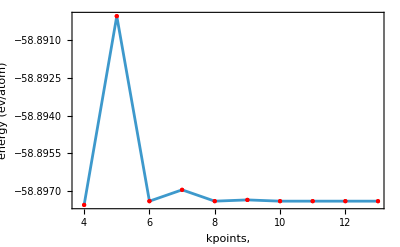

```mathematica
ListPlot[kpdat,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"kpoints,","energy (ev/atom)"}]
```

We have to check the convergence of this caltulation.

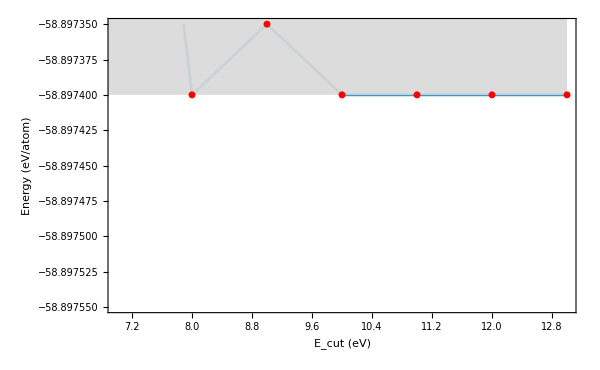

```mathematica
kpdat//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16},
PlotRange->{{#[[4,1]], #[[-1,1]]},{Min[#[[All,2]]], #[[6, 2]]}},
Joined->True,
InterpolationOrder->1,
Epilog->{{LightGray,Opacity[0.9],Rectangle[{#[[1, 1]], #[[-1,2]]},{#[[-1,1]],#[[-1,2]]+10^-3}]},
{Red,AbsolutePointSize[5],Point[#]}},
ImageSize->600,
Epilog->{Red,AbsolutePointSize[5], Point[#]}]&
```

We get <1 meV/atom convergency

## Equation of states for Si - fcc using DFTB +

```mathematica
SetDirectory["/home/angeldavid/wrk/Assigment/Diamond/eos/"];
```

```mathematica
Range[3.4176,3.7024,0.04]
```

{3.4176,3.4576,3.4976,3.5376,3.5776,3.6176,3.6576,3.6976}

```mathematica
datacell=Import["cell.dat"];
```

```mathematica
datacell
```

{{3.4176,-117.581},{3.4576,-117.704},{3.4976,-117.776},{3.5376,-117.8},{3.5776,-117.782},{3.6176,-117.724},{3.6576,-117.629},{3.6976,-117.502}}

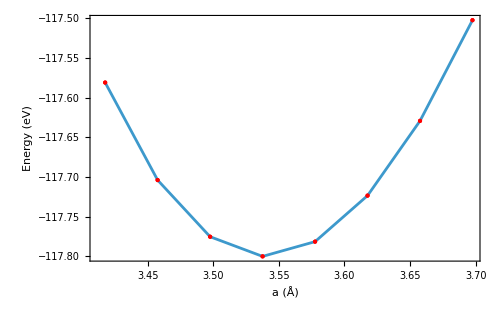

```mathematica
ListPlot[datacell,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"a (Å)","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImageSize->500
]
```

```mathematica
:
```

We need to transform the data to volume vs energy. For the C-fcc based on the POSCAR we have this:

```mathematica
a1=a{1/2,1/2,0.0};
a2=a{0,1/2,1/2};
a3 =a{1/2,0,1/2};
```

Then the volume of the cell is:

```mathematica
a1.(a2×a3)
```

0.+a^3/4

```mathematica
cell = datacell//Map[{(#[[1]])^3/4,#[[2]]}&,#]&
```

{{9.97938,-117.581},{10.3339,-117.704},{10.6967,-117.776},{11.0679,-117.8},{11.4476,-117.782},{11.8359,-117.724},{12.2329,-117.629},{12.6386,-117.502}}

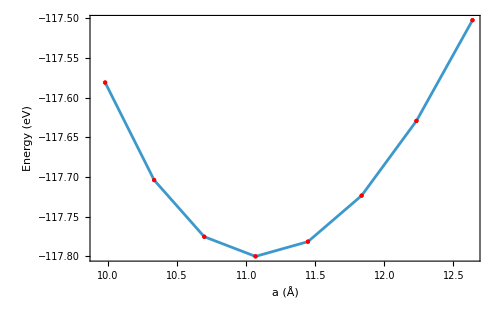

```mathematica
ListPlot[cell,
PlotRange->All,
Joined->True,
Mesh->Full,
MeshStyle->{Directive[PointSize[Medium],Red]},
Frame->True,
FrameLabel->{"a (Å)","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImageSize->500
]
```

Let' s fit data to BM-EOS

```mathematica
e= e0+(9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' +((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)));
```

This is not correct.

```mathematica
e0+(9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' +((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model = k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2
```

k[1]+k[2]/v^(2/3)+k[3]/v^(4/3)+k[4]/v^2

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm = NonlinearModelFit[cell,model,parameters,v];
```

```mathematica
nlm[v]
```

-67.1993-1055.24/v^2+1675.64/v^(4/3)-545.918/v^(2/3)

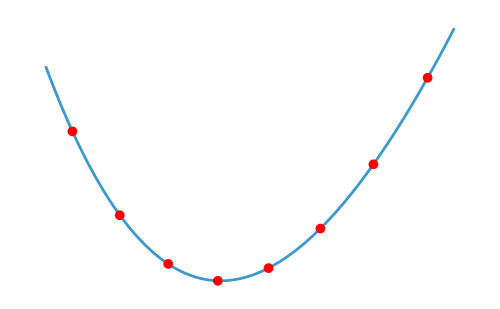

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2,(cell[[All,1]]//Max)+0.2},Epilog->{AbsolutePointSize[7],Red,Point[cell]},
Axes->None,
PlotRange->All,
FrameLabel->{"a (Å)","Energy (eV)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImageSize->500
]
```

```mathematica
nlm["RSquared"]
```

1.

Optimal Volume

```mathematica
opvol = FindMinimum[nlm[v],{v,11.06}]
```

{-117.8,{v→11.0887}}

```mathematica
opvol[[2]]
```

{v→11.0887}

```mathematica
bulkm=v D[nlm[v],{v,2}]/.opvol[[2]]
```

3.36831

The B_0 has units of pressure, here it expresed in units of [eV/Å^3], then in i.u. [N/m^2] =[Pa]:

```mathematica
UnitConvert[Quantity[bulkm,"Electronvolts"/("Angstroms")^3],"GigaPascals"]
```

539.662 GPa

Now we compute the bulk modulus pressure derivative

```mathematica
bulkpd= -v/bulkm D[v[D[nlm[v],{v,2}],v]]
```

-0.296885 v v[-6331.43/v^4+5213.11/v^(10/3)-606.575/v^(8/3),v]

```mathematica
sol = Solve[{e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,v0,B'}]
```

{{e0→31.4318,B0→-539.288,v0→1.25932,B'→5.74181},{e0→-117.8,B0→3.36831,v0→11.0887,B'→3.59152}}

By looking to the plot of the EOS, we know that v0 is ~11.07, then the 2st solution is the correct

```mathematica
Solve[v0==a^3/4,a]/.sol[[2]]
```

{{a→-1.76991+3.06557 ⅈ},{a→3.53982},{a→-1.76991-3.06557 ⅈ}}

Finally, the optimal lattie parameter of Si-fcc using DFTB+ is 5.39437 Å

A bulk modulus negative is how much soft is the material, thin about the submarine

## Density of States (DOS) for silicon fcc using DFTB+

```mathematica
SetDirectory["/home/angeldavid/wrk/Assigment/Diamond/eos/"];
```

```mathematica
dos=Import["dos_totalkp6.dat"];
```

```mathematica
ef=dos[[1,3]]
```

-3.558

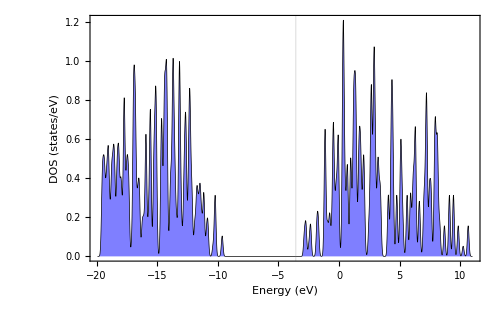

```mathematica
dos=Import["dos_totalkp6.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

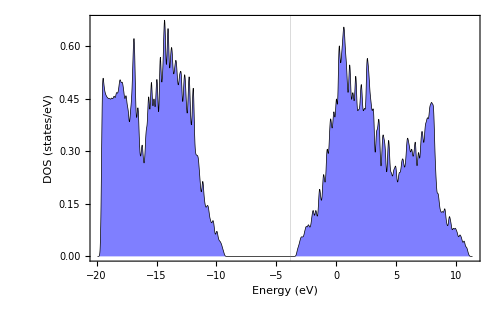

```mathematica
dos=Import["dos_totalkp20.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

Let' s do the calculation with more k points

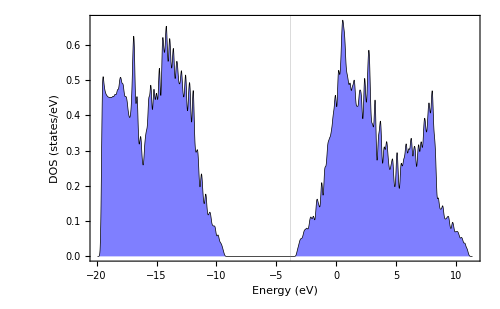

```mathematica
dos=Import["dos_totalkp22.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

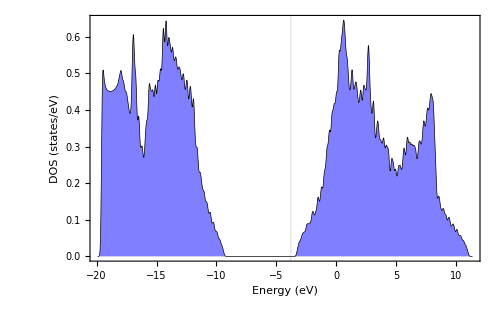

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->All

]
```

Let’s do a zoom around the fermi level

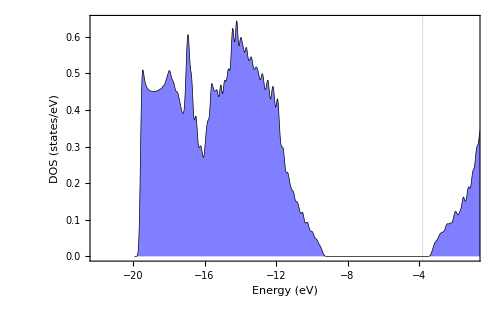

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{{-22,-1},All}

]
```

Here the fermi level is at  zero value dos states eV. Other programs use to put the fermi level at the lowest energy.

The conduction band is empty.

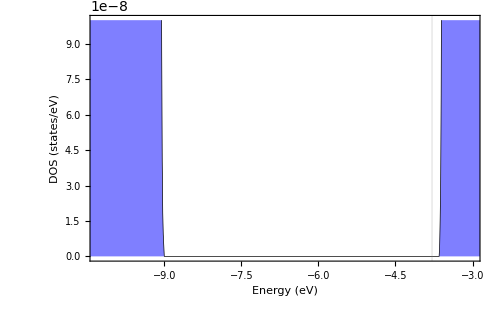

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
ListPlot[dos[[2;;-1]],
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{{-10.3,-3},{0,10^-7}}

]
```

```mathematica
{{-3.647159167697829,-2.3646134204456424*^-11}-{-8.990383241625638,-2.3646134204456424*^-11}}
```

{{5.34322,0.}}

Then  the bandgap or E_g is 5.34  eV. If there is a bandgap this material is an isolator. the left of the fermi level is the valance  and on the right for the bandgap is the conduction band and it is usually empty.

In this case we observe a bandgap around the fermi level, i.e., there are no energy levels near the fermi level, thus the material is isolator.

The density of states is telling me the amount of electronic states we can have high and low concentration of electronic states.

We can check how many valance electrons this system has . For that we integrate the density of states, all the range below the fermi level.  We have in total 8 electrons.

Now let’s compute the partial density of states for Si-fcc using DFTB+.

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
doss=Import["dos_C.s.dat"];
dosp=Import["dos_C.p.dat"];
(*dosd=Import["dos_C.d.dat"];*)
```

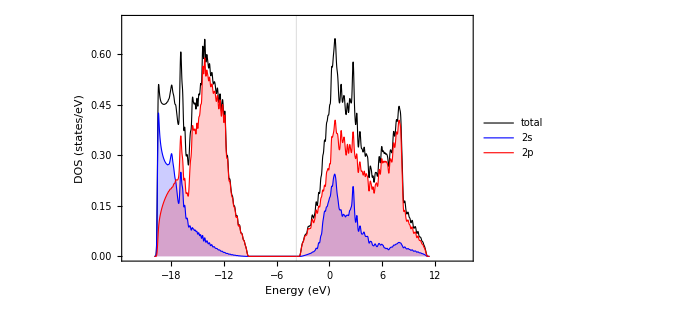

```mathematica
ListPlot[{dos[[2;;-1]],doss,dosp},
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Filling->{2->Axis,3->Axis},
(*FillingStyle->Directive[Opacity[0.5],Blue],*)
PlotStyle->{{AbsoluteThickness[0.8],Black},{AbsoluteThickness[0.8],Blue},{AbsoluteThickness[0.8],Red}},
ImageSize->500,
PlotLegends->Placed[{"total","2s","2p"},{Scaled[{0,0.75}],{0,0.5}}],
PlotRange->{{-22.9,15.6},{0,0.7}}

]
```

```mathematica
ListPlot[{dos[[2;;-1]],doss,dosp,dosd},
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)","DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->15},
Filling->{2->Axis,3->Axis,4->Axis},
(*FillingStyle->Directive[Opacity[0.5],Blue],*)
PlotStyle->{{AbsoluteThickness[0.8],Black},{AbsoluteThickness[0.8],Blue},{AbsoluteThickness[0.8],Red},{AbsoluteThickness[0.8],Green}},
ImageSize->500,
PlotLegends->Placed[{"total","3s","3p","3d"},{Scaled[{0,0.75}],{0,0.5}}],
PlotRange->{{-22.9,15.6},{0,3}}

]
```

ListPlot::lpn: {{{-19.93,1.45846×10^-7},{-19.92,4.43316×10^-7},{-19.91,1.00919×10^-6},{-19.9,2.11079×10^-6},{-19.89,4.17564×10^-6},{-19.88,8.02832×10^-6},{-19.87,0.0000150269},«37»,{-19.49,0.50117},{-19.48,0.506112},{-19.47,0.508745},{-19.46,0.509488},{-19.45,0.508756},{-19.44,0.506933},«3082»},{«1»},{«1»},{}} is not a list of numbers or pairs of numbers.

Here add analysis of the PDOS.

## The Band Structure of Si-fcc using DFTB+

From the SeekPath website, we can compute the first BZ using the optimal POSCAR from the computed ground

We are going to compute the band structure along L→Γ→X→K→W→Γ. For this use the script band_tot.dat that will generate the file band_tot.dat

```mathematica
SetDirectory["/home/angeldavid/wrk/Assigment/Diamond/eos/"];
```

```mathematica
databands=Import["band_tot.dat"];
```

Then we need the fermi level for that

```mathematica
dos=Import["dos_totalkp26.dat"];
ef=dos[[1,3]];
```

```mathematica
databands//Dimensions
```

{101,9}

In the high simmetry paths, There is 19 bands-energy levels (ϵ_nk), 101 are the divisions , remember we put 1,20,20,20,20 at the beguining of the path (it is the discretization of the k axis)in the xbands.sh

```mathematica
databands[[1]] (*these are the energy levels for k=1*)
```

{1,-18.051,-18.046,-11.874,-11.874,-0.709,1.298,1.298,11.048}

```mathematica
databands[[2]] (*and so on for k =101*)
```

{2,-18.279,-17.793,-11.864,-11.864,-0.713,1.278,1.278,10.974}

```mathematica
databands[[-1]] (*and this is the last k point k=101*)
```

{101,-19.574,-9.347,-9.347,-9.347,-3.309,-3.309,-3.309,-0.003}

```mathematica
bands = databands//Map[#[[2;;-1]]-ef&,#]&//Transpose;
```

```mathematica
bands[[1]]
```

{-14.2628,-14.4908,-14.6988,-14.8828,-15.0468,-15.1908,-15.3148,-15.4208,-15.5108,-15.5848,-15.6448,-15.6918,-15.7268,-15.7518,-15.7688,-15.7788,-15.7838,-15.7858,-15.7868,-15.7858,-15.7858,-15.7858,-15.7868,-15.7858,-15.7818,-15.7728,-15.7568,-15.7298,-15.6908,-15.6378,-15.5678,-15.4798,-15.3718,-15.2428,-15.0918,-14.9168,-14.7168,-14.4908,-14.2388,-13.9588,-13.6518,-13.7278,-13.7928,-13.8468,-13.8918,-13.9258,-13.9498,-13.9648,-13.9698,-13.9658,-13.9538,-13.9328,-13.9058,-13.8718,-13.8338,-13.7908,-13.7458,-13.7008,-13.6568,-13.6168,-13.5808,-13.5798,-13.5778,-13.5748,-13.5688,-13.5628,-13.5538,-13.5438,-13.5328,-13.5198,-13.5048,-13.4888,-13.4698,-13.4498,-13.4288,-13.4048,-13.3788,-13.3508,-13.3208,-13.2888,-13.2548,-13.4358,-13.6828,-13.9628,-14.2458,-14.5128,-14.7568,-14.9718,-15.1588,-15.3168,-15.4478,-15.5528,-15.6348,-15.6948,-15.7368,-15.7628,-15.7778,-15.7848,-15.7868,-15.7868,-15.7858}

```mathematica
bands//Dimensions
```

{8,101}

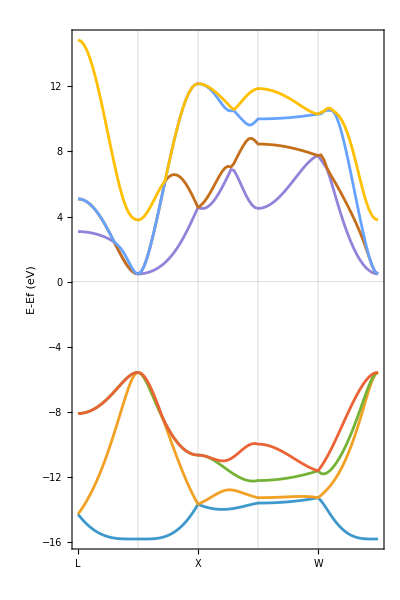

```mathematica
bands[[1;;-1]]//ListPlot[#,
Joined->True,
Frame->True,
FrameLabel->{None,"E-Ef (eV)"},
GridLines->{{21,41,61,81},{0}},
FrameTicks->{{{1,"L"},{21,"Γ"},{41,"X"},{61,"K"},{81,"W"},{101,"Γ"}},True},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotRange->{{1,101},All},
Axes->False,
AspectRatio->1.5
]&
```

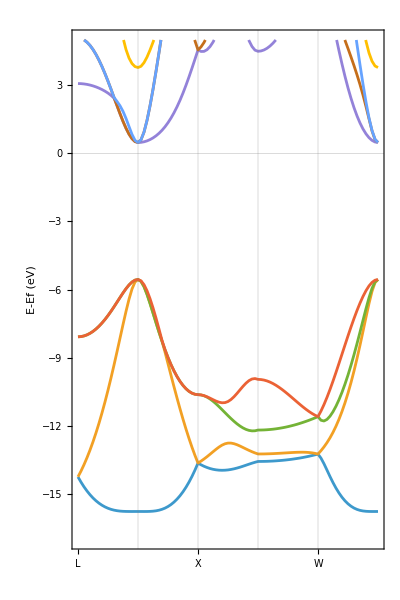

```mathematica
bands[[1;;-1]]//ListPlot[#,
Joined->True,
Frame->True,
FrameLabel->{None,"E-Ef (eV)"},
GridLines->{{21,41,61,81},{0}},
FrameTicks->{{{1,"L"},{21,"Γ"},{41,"X"},{61,"K"},{81,"W"},{101,"Γ"}},True},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotRange->{{1,101},{-17,5}},
Axes->False,
AspectRatio->1.5
]&
```

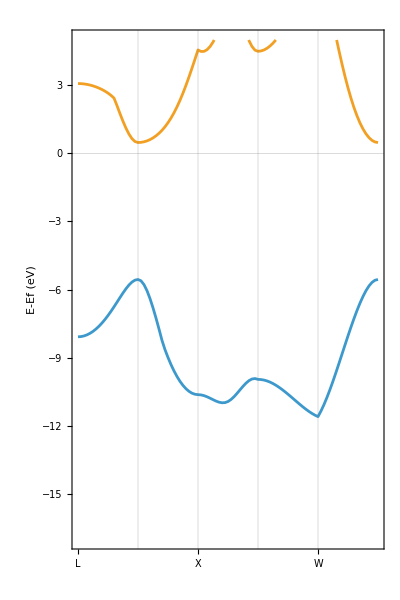

```mathematica
bands[[4;;5]]//ListPlot[#,
Joined->True,
Frame->True,
FrameLabel->{None,"E-Ef (eV)"},
GridLines->{{21,41,61,81},{0}},
FrameTicks->{{{1,"L"},{21,"Γ"},{41,"X"},{61,"K"},{81,"W"},{101,"Γ"}},True},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotRange->{{1,101},{-17,5}},
Axes->False,
AspectRatio->1.5
]&
```

Direct band, the highest value of the k space is the same as the lowest k value of the conduction band.  both are on the same gamma point. THis is incorrect, Si has indirect band, it has to be with the conservation of momentum and phonons.

compute the highest ocuppied band

```mathematica
hob = bands[[{4}]][[1]] //Interpolation[#]&(*stract the blue band/line*)
```

InterpolatingFunction[…]

```mathematica
lub = bands[[{5}]][[1]]//Interpolation[#]&
```

InterpolatingFunction[…]

```mathematica
FindMaximum[hob[x],{x,20}]
```

{-5.55821,{x→20.8813}}

```mathematica
FindMinimum[lub[x],{x,21}]
```

{0.477786,{x→21.2502}}

Then the bandgap E_g is

```mathematica
0.4777859362158069-(-5.558210494378982)
```

6.036